```mathematica
Style["NDSolve solution",20]
```

NDSolve solution

```mathematica
Clear[u,x,y,t,k,q,u0]
(*defining the heat equation and the contour conditions*)
eqn=D[u[x,y,t],{t,1}]-k D[u[x,y,t],{x,2}]-k D[u[x,y,t],{y,2}]==q[x,y,t];
cc1=u[x,y,0]==u0[x,y];
cc2=u[0,y,t]==0;
cc3=u[1,y,t]==0;
cc4=u[x,0,t]==0;
cc5=u[x,1,t]==0;
k=0.1;

u0[x_,y_]=(Sin[Pi x]Sin[Pi y])(*(1-Cos[Pi (2x-1)]*(1-y)+y)/2*);
q[x_,y_,t_]=0;
Plot3D[u0[x,y],{x,0,4},{y,0,4}]
tf=1;
uu=u/.NDSolve[{eqn,cc1,cc2,cc3,cc4,cc5},u,{x,0,1},{y,0,1},{t,0,tf}][[1]]
Manipulate[Plot3D[uu[x,y,t],{x,0,1},{y,0,1},ImageSize->600,PlotRange->{0,1}],{t,0,tf}]
```

-Graphics3D-

InterpolatingFunction[{{0., 1.}, {0., 1.}, {0., 1.}}, <>]

```mathematica
Style["Third order error analysis",20]
```

Third order error analysis

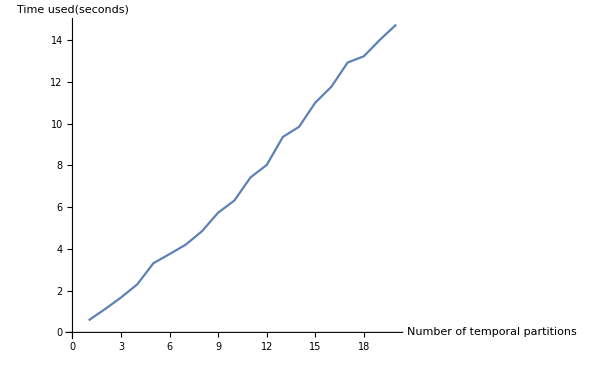

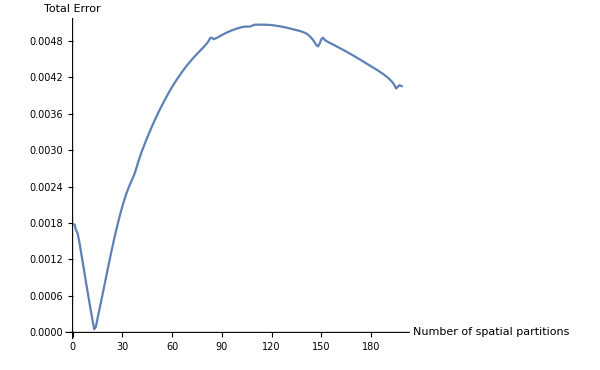

```mathematica
Clear[f,x,y,yy,t,Y,M,NN,w,Y0,xn,tn,X,T,RK,nx,a,tf,F,a1,a2,krk,krk1,krk2,MM,krk3,krk4,XX,aa1,aa2,W,v,MT]
X={};
T={};
MT={};
f[x_,y_,t_]:=k(D[u[x,y,t],{x,2}]+D[u[x,y,t],{y,2}]);
(*defining variables and parameters*)
x2=1;
x1=0;
y2=1;
y1=0;
ti=0;
tf=1;
pk=0.6;
qk=1-p;
rk=3;
sk=8;
d=0.001;
c=0.2;
pk=0.6;
qk=1-p;
rk=3;
sk=8;
d=0.001;
c=0.2;


aa1=0.5;
aa2=1-aa1;
a1=2.5/6;
a2=3/6;
a3=1-a1-a2;
M={};
NN=5;

Tempo={};
Do[AppendTo[Tempo,Timing[

JJ=15;(*5n*)
(*definitions*)
xn:=(2x2-x1)/(JJ-1);
yn:=(2y2-y1)/(JJ-1);
tn:=(tf-ti)/(NN-1);
X=Table[x,{x,x1,2x2-xn,xn}];
Y=Table[y,{y,y1,2y2-yn,yn}];
T=Table[t,{t,ti,tf,tn}];
W={w};
k=0.1;
p:=k*tn/(xn^2);
pk=0.6;
qk=1-p;
rk=3;
sk=8;
d=0.001;
c=0.2;
Y0=Table[u0[X,Y[[j]]],{j,1,JJ-1}];
Y0=Flatten[Y0];
w=Y0;
W={Y0};


(*Temporal evolution matrix*)

A={};
MT1=Table[{},(JJ-1)];

MZ=0IdentityMatrix[(JJ-1)];
ML=p*IdentityMatrix[(JJ-1)];
MC=-4p*IdentityMatrix[(JJ-1)];
MC[[1,(JJ-1)]]=p;
MC[[(JJ-1),1]]=p;
Table[MC[[j,j+1]]=p,{j,1,(JJ-2)}];
Table[MC[[j,j-1]]=p,{j,2,(JJ-1)}];
Do[A=Table[MZ,(JJ-1)];
A[[i]]=MC;
If[i>1,A[[i-1]]=ML];
If[i==1,A[[(JJ-1)]]=ML];
If[i<(JJ-1),A[[i+1]]=ML];
If[i==(JJ-1),A[[1]]=ML];
MT1[[i]]=Flatten[Join[Table[A[[j]],{j,1,(JJ-1)}]],1],{i,1,(JJ-1)}];
MT=Join[Table[Flatten[Join[Table[MT1[[j,i]],{j,1,(JJ-1)}]],1],{i,1,(JJ-1)^2}]];

F[t_,w_,tn_]:=Module[{},
 MT.w];
 
RK[3][F_,t_,w_,tn_]:=Module[{},

krk1=F[t,w,tn];
krk2=F[t+tn,w+krk1/2,tn];
krk3=F[t+rk,w+sk*krk2/2+(rk-sk)*krk1/2,tn];
w+(a1*krk1+a2*krk2+a3*krk3)];


(*solutions*)
Clear[WW,n];
WW={};
Do[
AppendTo[W,RK[3][F,t,W[[n]],tn]],
{n,1,NN-1}];

Do[
AppendTo[WW,Table[Table[Partition[W[[n]],JJ-1][[i,j]],{i,1,JJ-1}],{j,1,JJ-1}]];
,{n,1,NN}];
Clear[Uksn,uuRK];
Uksn=Flatten[Table[{{X[[i]],Y[[j]],T[[n]]},WW[[n,i,j]]},{n,1,NN},{i,1,(JJ-1)},{j,1,(JJ-1)} ],2];uuRK=Interpolation[Uksn];
Animate[Plot3D[uuRK[x,y,t],{x,x1,x2},{y,y1,y2},PlotPoints->15,ImageSize->400,PlotRange->{0,1}],{t,0,tf},AnimationRunning->False];
Manipulate[ListPlot3D[WW[[i]],PlotRange->{-1,1}],{i,1,NN,1}];

(*error*)
Clear[WW3,n];
WW3={};
t=0;
W={Y0};
erro={};
errot={};
(*ordem3*)


xn:=(2x2-x1)/(JJ-1);
yn:=(2y2-y1)/(JJ-1);
tn:=(tf-ti)/(NN-1);
X=Table[x,{x,x1,2x2-xn,xn}];
Y=Table[y,{y,y1,2y2-yn,yn}];
T=Table[t,{t,ti,tf,tn}];
Y0=Table[u0[X,Y[[j]]],{j,1,JJ-1}];
Y0=Flatten[Y0];
w=Y0;
W={Y0};


Do[AppendTo[W,RK[3][F,t,W[[n]],tn]],{n,1,NN-1}];
Do[AppendTo[WW3,Table[Table[Partition[W[[n]],JJ-1][[i,j]],{i,1,JJ-1}],{j,1,JJ-1}]],{n,1,NN}];
UU3=Flatten[Table[{{X[[i]],Y[[j]],T[[n]]},WW3[[n,i,j]]},{n,1,NN},{i,1,JJ-1},{j,1,JJ-1} ],2];
uu3=Interpolation[UU3,InterpolationOrder->2];
dif3=Abs[uu3[x,y,T]-uu[x,y,T]];
Do[AppendTo[erro,Max[FindMaximum[dif3[[i]],{{x,0.5},{y,0.5}},AccuracyGoal->0.00001,PrecisionGoal->0.00001]][[1]]],{i,2,NN,1}];][[1]]]
,{NN,10,200,10}]





im1=ListPlot[Tempo,ImageSize->600,Joined->True,AxesLabel->{"Number of temporal partitions","Time used(seconds)"}]
im2=ListPlot[erro,ImageSize->600,Joined->True,AxesLabel->{"Number of spatial partitions","Total Error"}]
```